# Numerical Solution of the Lieb-Liniger Equations

In this notebook, all the equations are referred to “Lieb, Liniger - Exact Analysis of an Interacting Bose Gas, Phys. Rev. 130, 1605, year 1963”, abbreviated as “LL”.

## Method for solving Fredholm equations of the Second kind

This method is taken from “S. Rahbar and E. Hashemizadeh, A Computational Approach to the Fredholm Integral Equation of the Second Kind” in “Proceedings of the World Congress on Engineering 2008 Vol II WCE 2008, July 2 - 4, 2008, London, U.K.”, ISBN:978-988-17012-3-7.

This method finds the numerical solution to the integral equation

f(x)=g(x)+ ∫_a^b K(x,y)f(y)ⅆy

BoundFunction: This module takes the function f as input and as output gives the function f in the interval [a,b] and zero otherwise.

Fredholm2ndKind: Gives the numerical solution of the Fredholm equation in the interval [a,b]. This takes as input the extremes of integration a and b, the kernel K(x,y), g(x) and the number, n, of subdivision of the integration interval which is used in the numerical solution. (see this link)

Fredholm2ndKindOut:  Gives the numerical solution of the Fredholm equation in the interval [c,d] outside of [a,b].This takes as input the extremes of integration a and b, the kernel K(x,y), g(x), the number, n, of subdivision of the integration interval [a,b] which is used in the numerical solution, the extreme of integration c and d of the interval outside [a,b] and the number of subdivisions of [c,d].

```mathematica
BoundFunction[f_,a_,b_]:=
Function[
Piecewise[{
{0.,#<a},
{0.,#>b},
{f[#],True}}]
];

(*Options[Fredholm2ndKind]={Method->Automatic};
Fredholm2ndKind[{a_,b_,k_,g_},n_?IntegerQ,OptionsPattern[]]:=
Block[{step,SI,GI,KMatrix,W,DMatrix,f,deltaX,delta,fI,ftemp},
step=(b-a)/n;
SI=Range[a,b,step];
GI=g/@SI;
KMatrix=Outer[k,SI,SI];
W={step/2}~Join~ConstantArray[step,n-1]~Join~{step/2};
DMatrix=DiagonalMatrix[W];
fI=LinearSolve[IdentityMatrix[n+1]-KMatrix.DMatrix,GI];
f=If[OptionValue[Method]===NoInterpolation,
fI,
BoundFunction[Interpolation[Transpose@{SI,fI}],a,b]];
f];*)

Options[Fredholm2ndKind]={Method->Automatic};
Fredholm2ndKind[{a_,b_,k_,g_},n_?IntegerQ,OptionsPattern[]]:=
Block[{step,SI,GI,KMatrix,W,DMatrix,f,deltaX,delta,fI,ftemp},
step=(b-a)/n;
SI=Range[a,b,step];
GI=g/@SI;
KMatrix=Outer[k,SI,SI];
W={step/2}~Join~ConstantArray[step,n-1]~Join~{step/2};
DMatrix=DiagonalMatrix[W];
deltaX[x_?NumericQ]:=W.(k[x,#]&/@SI)-NIntegrate[k[x,y],{y,a,b}];delta=deltaX/@SI;
fI=LinearSolve[IdentityMatrix[n+1]+(DiagonalMatrix[delta]-KMatrix.DMatrix),GI];
f=If[OptionValue[Method]===NoInterpolation,
fI,
BoundFunction[Interpolation[Transpose@{SI,fI}],a,b]];
f];

Fredholm2ndKindOut[{a_,b_,k_,g_},n_?IntegerQ,{c_,d_},m_?IntegerQ,fIni_:True]:=
Block[{fInTempi,stepIn,SIni,stepOut,SOuti,GOuti,KMatrixOut,fOuti},
(* Variable inside the interval [a,b] *)
stepIn=(b-a)/n;
SIni=Range[a,b,stepIn]; (*i-th component of the interval*)
fInTempi=If[fIni===True,
Fredholm2ndKind[{a,b,k,g},n,Method->NoInterpolation],
fIni];
(* Variable and functions outside the interval [a,b] *)
stepOut=(d-c)/m;
SOuti=Range[c,d,stepOut]; (*i-th component of the interval*)
GOuti=g/@SOuti; (*i-th component of the g*)
KMatrixOut=Outer[k,SOuti,SIni]; (*Matrix form of k*)
fOuti=GOuti+stepIn*(KMatrixOut.fInTempi-(KMatrixOut[[All,1]]*fInTempi[[1]]+KMatrixOut[[All,n+1]]*fInTempi[[n+1]])/2);
BoundFunction[Interpolation[Transpose[{SOuti,fOuti}]],c,d]];
```

## Lieb-Liniger model

Procedure:
We start by numerically solving the renormalized equation for the density of states (DOS) (see Eq. (LL3.18)),

g(x)=1/(2 π)+λ/π∫_-1^1 (g(y))/(λ^2+(x-y)^2)ⅆy, x∈[-1,1], g(x)=0 otherwise.

The renormalized equation for the spectrum is (see Eq. (YY33))

e(x)=-m+x^2+λ/π∫_-1^1 (e(y))/(λ^2+(x-y)^2)ⅆy
In this case we can use the same kernel of g(x).

```mathematica
m=0.5; (*Renormalized chemical potential*)
n=1000;(*number of discretization*)
```

```mathematica
gLL[x_]:=1/(2*Pi);
gSolve[λ_]:=Block[{KLL,Out},
KLL[x_,y_]:=λ/(Pi*(λ^2+(x-y)^2));
Out =Fredholm2ndKind[{-1.,1.,KLL,gLL},n];
Out]
(*Manipulate[
g=gSolve[λ];
Plot[{g[x],Sqrt[1-x^2]/(2*Pi*λ)},{x,-Pi,Pi},Frame->True,Axes->False,PlotRange->{0,4}],{λ,0.06,0.2}]*)
eLL[x_]:=-m+x^2;
eSolve[λ_,a_,b_]:=Module[{KLL,fIni, fIn,fLeft,fRight,Out},
KLL[x_,y_]:=λ/(Pi*(λ^2+(x-y)^2));
fIni=Fredholm2ndKind[{-1.,1.,KLL,eLL},n,Method->NoInterpolation];
fIn=Interpolation[Transpose[{Table[i,{i,-1.,1.,2./n}],fIni}]];
fLeft=Fredholm2ndKindOut[{-1.,1.,KLL,eLL},n,{a,-1.},n,fIni];
fRight=Fredholm2ndKindOut[{-1.,1.,KLL,eLL},n,{1.,b},n,fIni];
Function[
Piecewise[{
{fLeft[#],a≤#<-1.},
{fIn[#],-1.≤#≤1.},
{fRight[#],1.<#≤b},
{0.,True}}]]
]
(* Approximate analytical solution *)
eAnalytical[x_,λ_]:=
Piecewise[{
{-1/(3λ)(1-x^2)^(3/2),-1.≤x≤1.},
{Abs[x]*Sqrt[x^2-1],True}}];
(*Manipulate[
e=eSolve[λ];
Plot[{e[x],eAnalytical[x,λ]},{x,-2.,2.},Frame->True,Axes->False,Exclusions->None],{λ,0.06,0.2}]*)
```

## Yang-Yang model:

```mathematica
eYY[μ_,t_,λ_,a_,b_,n_,precision_]:=
Block[{step,xi,ϵ0,ϵ0i,kc,kci,kT,ϵi,ϵiprev,converged,ϵconverged},
converged=0;
step=(b-a)/(n-1);
xi = Range[a,b,step];
ϵ0[k_]:=-μ+k^2;
ϵ0i=ϵ0/@xi;
kc[x_,y_]:=λ/(Pi*(λ^2+(x-y)^2));
kci=Outer[kc,xi,xi];
kT[ϵ_]:=t*Log[1+Exp[-ϵ/t]];
ϵconverged[Δϵ_]:=If[Abs[Δϵ]<precision,1,0];
ϵi=ϵ0i;
While[converged===0,
ϵiprev=ϵi;
(* Trapezoidal rule sum *)
ϵi=ϵ0i-step*(kci.(kT/@ϵiprev)-(kci[[All,1]]*kT[ϵiprev[[1]]]+kci[[All,n]]*kT[ϵiprev[[n]]])/2); 
converged=Times@@(ϵconverged/@(ϵiprev-ϵi));
];
ϵi]
gYY[μ_,t_,λ_,a_,b_,n_,precision_]:=Block[{eYYDiscrete,eYYfunction,k,g},
eYYDiscrete=eYY[μ, t, λ, a,b,n,precision];
eYYfunction=Interpolation[Transpose[{Table[i,{i,a,b,(b-a)/(n-1)}],eYYDiscrete}]];
g[x_]:=1/(2*Pi*(1+Exp[eYYfunction[x]/t]));
k[x_,y_]:=1/(1+Exp[eYYfunction[x]/t])*λ/(Pi*(λ^2+(x-y)^2));
Fredholm2ndKind[{a,b,k,g},n]
];
```

## Plots:

### Spectrum:

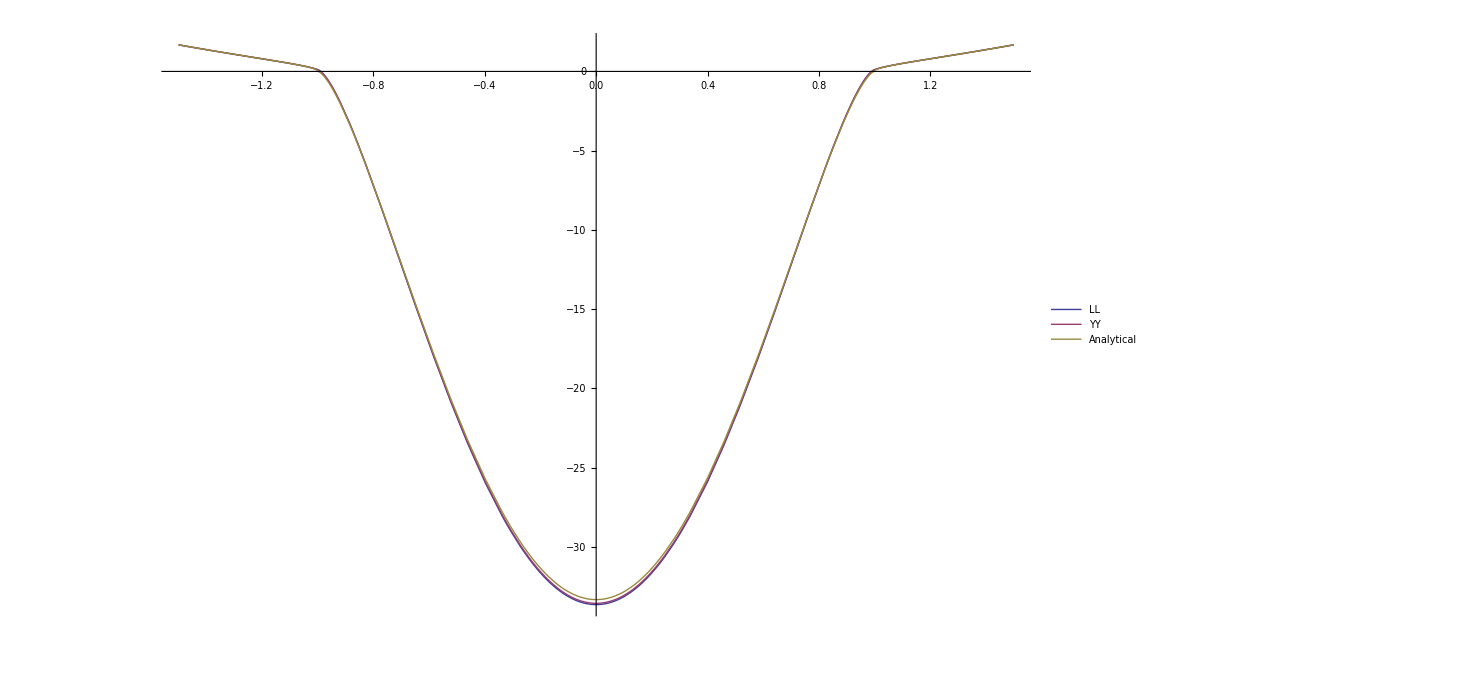

```mathematica
PlotSpectrumComparision[a_,b_,λ_, t_]:= Block[{eLLfunction,eYYDiscrete,eYYfunction},
(* Lieb-Liniger *)
eLLfunction=eSolve[λ,a,b];
(* Yang-Yang *)
eYYDiscrete=eYY[m, t, λ, a,b,n,N[1/n]];
eYYfunction=Interpolation[Transpose[{Table[i,{i,a,b,(b-a)/(n-1)}],eYYDiscrete}]];
(* Plot *)
Plot[{eLLfunction[x],eYYfunction[x],eAnalytical[x,λ]},{x,a,b},Exclusions->None,PlotLegends->{"LL","YY","Analytical"}]];
PlotSpectrumComparision[-1.5,1.5,0.01,0.01]
```

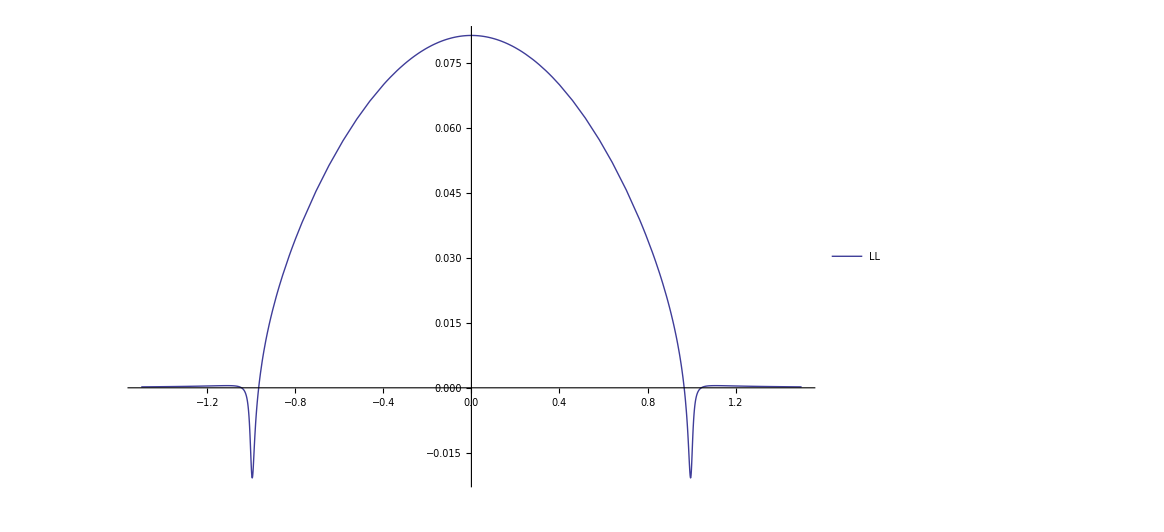

```mathematica
PlotSpectrumDiff[a_,b_,λ_, t_]:= Block[{eLLfunction,eYYDiscrete,eYYfunction},
(* Lieb-Liniger *)
eLLfunction=eSolve[λ,a,b];
(* Yang-Yang *)
eYYDiscrete=eYY[m, t, λ, a,b,n,N[1/n]];
eYYfunction=Interpolation[Transpose[{Table[i,{i,a,b,(b-a)/(n-1)}],eYYDiscrete}]];
(* Plot *)
Plot[{eYYfunction[x]-eLLfunction[x]},{x,a,b},Exclusions->None,PlotLegends->{"LL","YY","Analytical"}]];
PlotSpectrumDiff[-1.5,1.5,0.01,0.01]
```

### DOS:

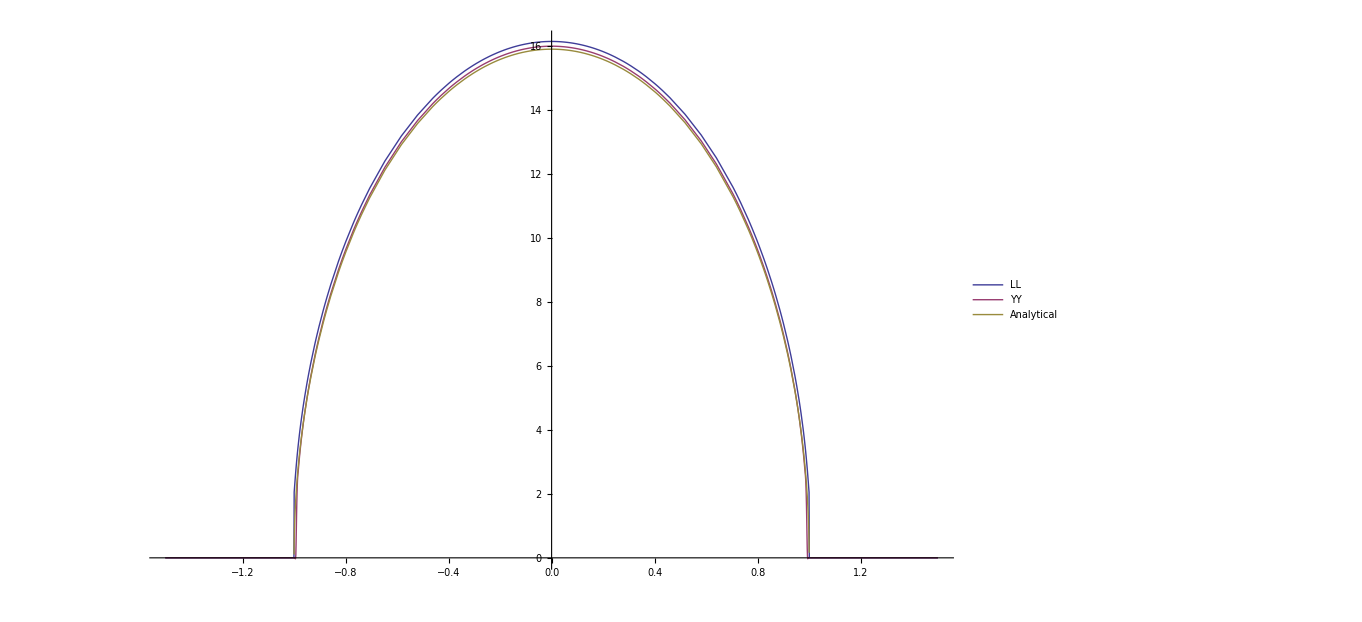

```mathematica
PlotDOSComparision[a_,b_,λ_, t_]:=Block[{gLLfunction,gYYfunction},
(* Lieb-Liniger *)
gLLfunction=gSolve[λ];
(* Yang-Yang *)
gYYfunction=gYY[m, t, λ, a,b,n,N[1/n]];
(* Plot *)
Plot[{gLLfunction[x],gYYfunction[x],Sqrt[1-x^2]/(2*Pi*λ)},{x,a,b},Exclusions->None,PlotLegends->{"LL","YY","Analytical"}]];
PlotDOSComparision[-1.5,1.5,0.01,0.01]
```

### Derviative of DOS by Chemical potential:

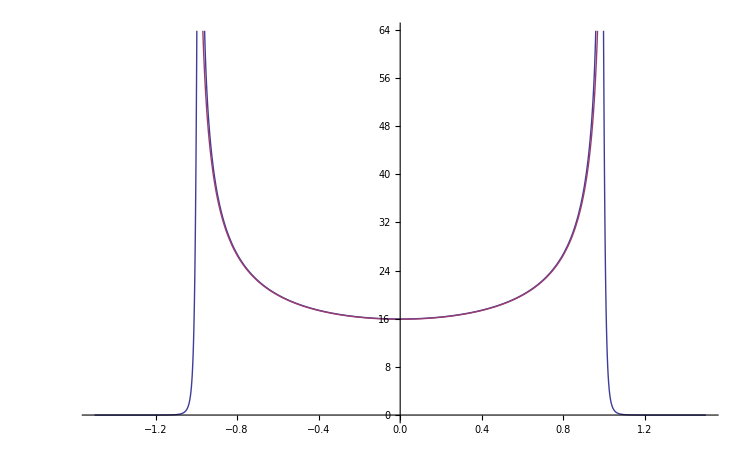

```mathematica
DmgYY[μ_,t_,λ_,a_,b_,n_,precision_]:=Block[{eYYDiscrete,eYYfunction,k,g,gYYfunction},
eYYDiscrete=eYY[μ, t, λ, a,b,n,precision];
eYYfunction=Interpolation[Transpose[{Table[i,{i,a,b,(b-a)/(n-1)}],eYYDiscrete}]];
gYYfunction=gYY[μ, t, λ, a,b,n,precision];
g[x_]:=2*Pi*Exp[eYYfunction[x]/t]/t*(gYYfunction[x])^2;
k[x_,y_]:=1/(1+Exp[eYYfunction[x]/t])*λ/(Pi*(λ^2+(x-y)^2));
Fredholm2ndKind[{a,b,k,g},n]
];
PlotDmgYY[a_,b_,λ_, t_]:=Block[{DmgYYfunction},
DmgYYfunction=DmgYY[m, t, λ, a,b,n,N[1/n]];
(* Plot *)
Plot[{DmgYYfunction[x],1/(2*Pi*λ*Sqrt[1-x^2])},{x,a,b},Exclusions->None]];
PlotDmgYY[-1.5,1.5,0.01,0.1]
```